/home/zack/Desktop/snakingoscillators

-Graphics-

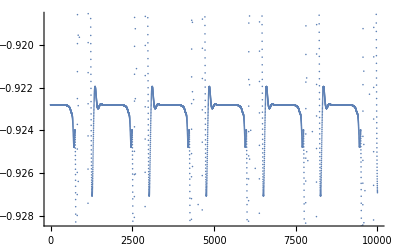

{{954},{2701},{4448},{6195},{6196},{7942},{7943},{9690}}

```mathematica
SetDirectory[NotebookDirectory[]]
filebase="data/test9";
dat=BinaryReadList[filebase<>"phases.npy","Real64"][[17;;-1]];
M=16;
theta=ArcTan[Partition[dat,4*M][[All,1;;M]],Partition[dat,4*M][[All,M+1;;2*M]]];
phi=ArcTan[Partition[dat,4*M][[All,2*M+1;;3*M]],Partition[dat,4*M][[All,3*M+1;;4*M]]];
Grid[{{ListDensityPlot[theta,AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->{-Pi,Pi},ColorFunctionScaling->False],ListDensityPlot[phi,AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->{-Pi,Pi},ColorFunctionScaling->False],ListPlot[Transpose[{Cos[phi[[All,1]]],Cos[theta[[All,1]]]}],PlotRange->{{-1,1},{-1,1}},ImageSize->300]}}]
ListPlot[Partition[dat,4*M][[All,1]]]
Position[Partition[dat,4*M][[All,1]],u_/;u>0.999]
```

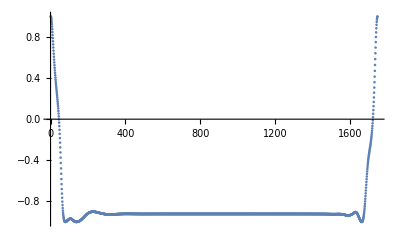

```mathematica
ListPlot[out[[All,1]],PlotRange->All]
```

```mathematica
out=Partition[dat,4*M][[954;;2701]];
Manipulate[ListPlot[{ArcTan[out[[n,1;;M]],out[[n,M+1;;2*M]]],ArcTan[out[[n,2*M+1;;3*M]],out[[n,3*M+1;;4*M]]]},PlotRange->{-Pi,Pi}],{n,1,Length[out],1}]
Export["data/chimera1.dat",Table[Prepend[out[[i]],0.1*(i-1)],{i,1,Length[out]}]]
```

data/chimera1.dat

```mathematica
vals=(#/#[[1]]&@Flatten[{#[[1;;M]]+I*#[[M+1;;2*M]],#[[2*M+1;;3*M]]+I*#[[3*M+1;;4*M]]}])&/@out;
out2=Flatten[{Re[#[[2;;M]]],Im[#[[2;;M]]],Re[#[[M+1;;2*M]]],Im[#[[M+1;;2*M]]]}]&/@vals;
Export["data/chimera1_rel.dat",Table[Prepend[out2[[i]],0.1*(i-1)],{i,1,Length[out2]}]]
```

data/chimera2_rel.dat

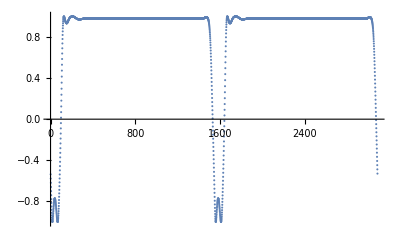

{{125},{126},{127},{199},{200},{201},{202},{203},{204},{205},{206},{207},{208},{209},{210},{211},{212},{213},{214},{1668},{1669},{1670},{1742},{1743},{1744},{1745},{1746},{1747},{1748},{1749},{1750},{1751},{1752},{1753},{1754},{1755},{1756}}

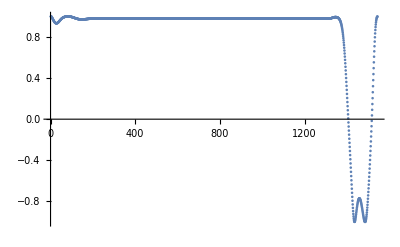

data/chimera4.dat

```mathematica
ListPlot[out2[[All,1]],PlotRange->All]
Position[out2[[All,1]],u_/;u>0.999]
out3=out2[[125;;1668]];
ListPlot[out3[[All,1]],PlotRange->All]
Export["data/chimera4.dat",Table[Prepend[out3[[i]],0.1*(i-1)],{i,1,Length[out3]}]]
```

```mathematica
SetDirectory[NotebookDirectory[]]
data=Import["chimera.dat"];
xs=data[[All,2;;10]];
ys=data[[All,11;;19]];
ws=data[[All,20;;29]];
vs=data[[All,30;;39]];
{xs[[1]], ys[[1]], ws[[1]], vs[[1]]}
```

/home/zack/Desktop/janus

{{0.999994,0.999994,0.999994,0.999988,0.999849,0.959871,0.377818,0.953899,0.999297},{-0.00343364,-0.00339093,-0.00345492,-0.00499574,-0.0173528,0.280439,-0.92588,0.300126,-0.0374934},{0.542543,0.551785,0.549702,0.549996,0.549638,0.54601,0.545303,-0.975791,0.100485,0.541594},{-0.840028,-0.833986,-0.835361,-0.835167,-0.835403,-0.837779,-0.838239,-0.218701,-0.994939,-0.84064}}

```mathematica
beta=0.25;
sigma=0.35;
gamma=1.0;
omega=1.0;
{x,y,w,v}={xs[[1]], ys[[1]], ws[[1]], vs[[1]]}
```

```mathematica
(xs[[2]]-xs[[1]])/0.1
```

{7.1×10^-6,5.9×10^-6,6.×10^-6,7.2×10^-6,0.0000864,-0.0865996,0.140506,0.0236148,0.0003845}

```mathematica
(ys[[2]]-ys[[1]])/0.1
```

{0.00215398,0.0018675,0.00185307,0.00146775,0.00505857,0.280892,0.0585914,-0.0761181,0.0103907}

```mathematica
(ws[[2]]-ws[[1]])/0.1
```

{-0.0010825,0.0014973,0.0016552,0.0015562,0.0014854,0.0010311,0.0267541,-0.0583142,-0.148706,0.0365621}

```mathematica
(vs[[2]]-vs[[1]])/0.1
```

{-0.0006991,0.0009906,0.0010896,0.0010252,0.0009775,0.0006724,0.0174659,0.278882,-0.0138938,0.023669}

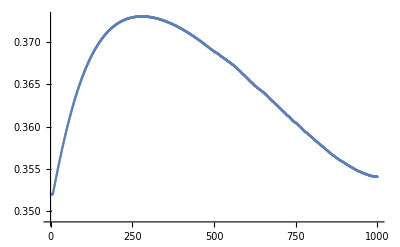

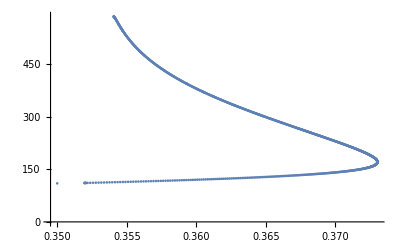

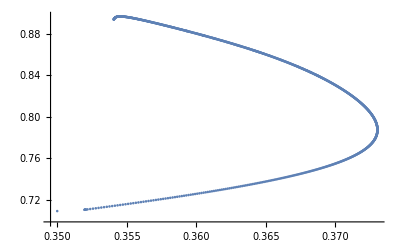

```mathematica
vals=Import["test.dat"];
ListPlot[vals[[1;;-2,1]]]
ListPlot[vals[[1;;-2,{1,8}]]]
ListPlot[vals[[1;;-2,{1,2}]]]
```